```mathematica
Quit[]
```

### Common

```mathematica
GammaMatrix[5]
```

GammaMatrix[5]

```mathematica
PR
```

{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
σ0=PauliMatrix[4];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];

GammaMatrix[0]={
{0,0,σ0[[1,1]],σ0[[1,2]]},
{0,0,σ0[[2,1]],σ0[[2,2]]},
{σ0[[1,1]],σ0[[1,2]],0,0},
{σ0[[2,1]],σ0[[2,2]],0,0}
};
GammaMatrix[1]={
{0,0,σ1[[1,1]],σ1[[1,2]]},
{0,0,σ1[[2,1]],σ1[[2,2]]},
{-σ1[[1,1]],-σ1[[1,2]],0,0},
{-σ1[[2,1]],-σ1[[2,2]],0,0}
};
GammaMatrix[2]={
{0,0,σ2[[1,1]],σ2[[1,2]]},
{0,0,σ2[[2,1]],σ2[[2,2]]},
{-σ2[[1,1]],-σ2[[1,2]],0,0},
{-σ2[[2,1]],-σ2[[2,2]],0,0}
};
GammaMatrix[3]={
{0,0,σ3[[1,1]],σ3[[1,2]]},
{0,0,σ3[[2,1]],σ3[[2,2]]},
{-σ3[[1,1]],-σ3[[1,2]],0,0},
{-σ3[[2,1]],-σ3[[2,2]],0,0}
};
γ0=GammaMatrix[0];
γ1=GammaMatrix[1];
γ2=GammaMatrix[2];
γ3=GammaMatrix[3];
γ[i_]:=GammaMatrix[i];
γv={γ0,γ1,γ2,γ3};
γ5=I*γ0.γ1.γ2.γ3;
I4=IdentityMatrix[4];
PL=1/2(I4-γ5);
PR=1/2(I4+γ5);

LDot[p_,q_]:=p[0]*q[0]-Sum[p[i]q[i],{i,3}];
LDot[p_List,q_List]:=p[[1]]*q[[1]]-Sum[p[[i]]q[[i]],{i,2,4}];
Mass[p_]:=Sqrt[LDot[p,p]];
SquaredMass[p_]:=LDot[p,p];

PropagatorDen[p_,m_,Γ_]:=Im/(SquaredMass[p]-m^2+I*m*Γ)
FermionPropagatorNum[p_,m_]:=(LDot[p,γ]+m*I4)
FermionPropagator[p_,m_,Γ_]:=FermionPropagatorNum[p,m]*PropagatorDen[p,m,Γ]
```

### Spinors

```mathematica
pmag[px_,py_,pz_]:=Sqrt[px^2+py^2+pz^2]
χp[px_,py_,pz_]=With[{pm=pmag[px,py,pz]},1/(√(2*pm*(pm+pz))){pm+pz,px+I*py}];
χm[px_,py_,pz_]=With[{pm=pmag[px,py,pz]},1/(√(2*pm*(pm+pz))){-px+I*py,pm+pz}];
χp[0,0,pz_]=If[pz<0,{0,1},{1,0}];
χm[0,0,pz_]=If[pz<0,{-1,0},{0,1}];

χp[0,0,0]={0,1};
χm[0,0,0]={-1,0};

ωp[e_,px_,py_,pz_]:=Sqrt[e+pmag[px,py,pz]];
ωm[e_,px_,py_,pz_]:=Sqrt[e-pmag[px,py,pz]];

χλ[{e_,px_,py_,pz_},1]:=χp[px,py,pz];
χλ[{e_,px_,py_,pz_},-1]:=χm[px,py,pz];
ωλ[{e_,px_,py_,pz_},1]:=ωp[e,px,py,pz];
ωλ[{e_,px_,py_,pz_},-1]:=ωm[e,px,py,pz];

SpinorU[p_,λ_]:=With[{ω1=ωλ[p,λ],ω2=ωλ[p,-λ],χ=χλ[p,λ]},{ω2 χ⟦1⟧,ω2 χ⟦2⟧,ω1 χ⟦1⟧,ω1 χ⟦2⟧}];
SpinorV[p_,λ_]:=With[{χ=χλ[p,-λ]},{-λ ωλ[p,λ]χ⟦1⟧,-λ ωλ[p,λ]χ⟦2⟧,λ ωλ[p,-λ]χ⟦1⟧,λ ωλ[p,-λ]χ⟦2⟧}];

SpinorUBar[p_,λ_]:=Dot[Conjugate[SpinorU[p,λ]],γ0];
SpinorVBar[p_,λ_]:=Dot[Conjugate[SpinorV[p,λ]],γ0]
```

```mathematica
SpinorUBar[{1,0,0,0},-1]
```

{-1,0,-1,0}

```mathematica
SpinorMany[n_,spinor_]:=Module[{ps,spinorsUp,spinorsDown},
ps=Table[PhaseSpace`Private`generateMomenta[10.0,{1.0,2.0,3.0}]⟦1⟧,{n}];
spinorsUp=Table[spinor[p,1],{p,ps}];
spinorsDown=Table[spinor[p,-1],{p,ps}];
{ps,spinorsUp,spinorsDown}
]
```

```mathematica
spinorUData=SpinorMany[10,SpinorU];
```

```mathematica
spinorVData=SpinorMany[10,SpinorV];
spinorUBarData=SpinorMany[10,SpinorUBar];
spinorVBarData=SpinorMany[10,SpinorVBar];
```

```mathematica
OutputDataMomenta[name_,data_]:=Module[{},
str="static const std::array<blackthorn::LVector<double>, N_TEST_PTS> "<> name <>" = {\n";
For[i=1,i<=Length[data],i++,
row=data[[i]];
str=str<>"blackthorn::LVector<double>{";
For[j=1,j<Length[data[[i]]],j++,
x=row[[j]];
str=str<>ToString[x,CForm]<>",";
];
x=Last[row];
str=str<>ToString[x,CForm]<>If[i==Length[data],"}\n","},\n"];
];
str=str<>"};";

str
];

OutputDataDVector[name_,data_]:=Module[{},
str="static const std::array<blackthorn::DVector<cmplx>, N_TEST_PTS> "<> name <>" = {\n";
For[i=1,i<=Length[data],i++,
row=data[[i]];
str=str<>"blackthorn::DVector<cmplx>{";
For[j=1,j<Length[data[[i]]],j++,
x=row[[j]];
str=str<>"cmplx{"<>ToString[Re[x],CForm]<>","<>ToString[Im[x],CForm]<>"},"
];
x=Last[row];
str=str<>"cmplx{"<>ToString[Re[x],CForm]<>","<>ToString[Im[x],CForm]<>If[i==Length[data],"}}\n","}},\n"];
];
str=str<>"};";

str
];
```

```mathematica
AllData={
{"U",SpinorMany[10,SpinorU]},
{"V",SpinorMany[10,SpinorV]},
{"UBAR",SpinorMany[10,SpinorUBar]},
{"VBAR",SpinorMany[10,SpinorVBar]}
};

Module[{i},
str="";
str=str<>"#include \"blackthorn/tensors.hpp\"\n";
str=str<>"#include<array>\n";
str=str<>"#include<cmath>\n";
str=str<>"static constexpr size_t N_TEST_PTS=10;\n";
str=str<>"using cmplx=std::complex<double>;\n\n";
For[i=1,i<=Length[AllData],i++,
NAME=AllData[[i]][[1]];
DATA=AllData[[i]][[2]];
str=str<>OutputDataMomenta["SPINOR_"<>NAME<>"_PS",DATA[[1]]]<>"\n\n";
str=str<>OutputDataDVector["SPINOR_"<>NAME<>"_U_WFS",DATA[[2]]]<>"\n\n";
str=str<>OutputDataDVector["SPINOR_"<>NAME<>"_D_WFS",DATA[[3]]]<>"\n\n";
];
str
]
```

### Polarizations

```mathematica
expr=1/(km*kt){0,kx*kz,ky*kz,-kt^2}//ReplaceAll[{km->Mag3[{e,kx,ky,kz}],kt->Trans[{e,kx,ky,kz}]}];
expr/.{ky->0}//Series[#,{kx,0,0},Assumptions->{kx>0,kz>0}]&//Normal;
Echo[%,"ϵ_1,k_T->0,k_z>0"];
expr/.{ky->0}//Series[#,{kx,0,0},Assumptions->{kx<0,kz<0}]&//Normal;
Echo[%,"ϵ_1,k_T->0,k_z<0"];

expr=1/kt{0,-ky,kx,0}//ReplaceAll[kt->Trans[{e,kx,ky,kz}]];
expr/.{ky->0}//Series[#,{kx,0,0},Assumptions->{kx>0,kz>0}]&//Normal;
Echo[%,"ϵ_2,k_T->0,k_z>0"];
expr/.{ky->0}//Series[#,{kx,0,0},Assumptions->{kx<0,kz<0}]&//Normal;
Echo[%,"ϵ_2,k_T->0,k_z>0"];
```

ϵ_1,k_T->0,k_z>0  {0,1,0,0}

ϵ_1,k_T->0,k_z<0  {0,1,0,0}

ϵ_2,k_T->0,k_z>0  {0,0,1,0}

ϵ_2,k_T->0,k_z>0  {0,0,-1,0}

```mathematica
Mag3[{e_,px_,py_,pz_}]:=Sqrt[px^2+py^2+pz^2];
Trans[{e_,px_,py_,pz_}]:=Sqrt[px^2+py^2];

pol3[k:{e_,kx_,ky_,kz_}]:=e/(m*km){km^2/e,kx,ky,kz}//ReplaceAll[{km->Mag3[k],m->Mass[k]}];
pol1[k:{e_,kx_,ky_,kz_}]:=1/(km*kt){0,kx*kz,ky*kz,-kt^2}//ReplaceAll[{km->Mag3[k],kt->Trans[k]}];
pol2[k:{e_,kx_,ky_,kz_}]:=1/kt{0,-ky,kx,0}//ReplaceAll[kt->Trans[k]];

pol1[{k0_,0,0,kz_}]:={0,1,0,0};
pol2[{k0_,0,0,kz_}]:={0,0,If[kz>0,1,-1],0};


pol[k_,1]:=1/(√2)(-pol1[k]-I*pol2[k]);
pol[k_,-1]:=1/(√2)(pol1[k]-I*pol2[k]);
pol[k_,0]:=pol3[k];
```

```mathematica
pol[{1,0,0,1},1]
pol[{1,0,0,1},-1]
```

{0,-1/(√2),-ⅈ/(√2),0}

{0,1/(√2),-ⅈ/(√2),0}

```mathematica
z
```

```mathematica
(*
   kt=0,kz>0,m>0,initial-state,spin=1
*)
```

```mathematica
pol[{1,0,0,-1/2},1]
pol[{1,0,0,-1/2},-1]
```

{0,-1/(√2),ⅈ/(√2),0}

{0,1/(√2),ⅈ/(√2),0}

```mathematica
Conjugate@pol[{1,0,0,-1},1]
```

{0,-1/(√2),-ⅈ/(√2),0}

```mathematica
{pol[{1,0,0,1},λ],{0,-λ/(√2),-s*I/(√2)}}//ReplaceAll[{λ->1,s->1}]
{pol[{1,0,0,1},λ],{0,-λ/(√2),-s*I/(√2)}}//ReplaceAll[{λ->-1,s->1}]
{Conjugate@pol[{1,0,0,1},λ],{0,-λ/(√2),-s*I/(√2)}}//ReplaceAll[{λ->1,s->-1}]
{Conjugate@pol[{1,0,0,1},λ],{0,-λ/(√2),-s*I/(√2)}}//ReplaceAll[{λ->-1,s->-1}]
```

{{0,-1/(√2),-ⅈ/(√2),0},{0,-1/(√2),-ⅈ/(√2)}}

{{0,1/(√2),-ⅈ/(√2),0},{0,1/(√2),-ⅈ/(√2)}}

{{0,-1/(√2),ⅈ/(√2),0},{0,-1/(√2),ⅈ/(√2)}}

{{0,1/(√2),ⅈ/(√2),0},{0,1/(√2),ⅈ/(√2)}}

```mathematica
PolMany[n_]:=Module[{ps,ϵp1,ϵ0,ϵm1},
ps=Table[PhaseSpace`Private`generateMomenta[10.0,{1.0,2.0,3.0}]⟦1⟧,{n}];
ϵp1=Table[pol[p,1],{p,ps}];
ϵ0=Table[pol[p,0],{p,ps}];
ϵm1=Table[pol[p,-1],{p,ps}];
{ps,ϵp1,ϵ0,ϵm1}
]
```

```mathematica
PolData=PolMany[10];
```

```mathematica
OutputDataMomenta[name_,data_]:=Module[{},
str="static const std::array<blackthorn::LVector<double>, N_TEST_PTS> "<> name <>" = {\n";
For[i=1,i<=Length[data],i++,
row=data[[i]];
str=str<>"blackthorn::LVector<double>{";
For[j=1,j<Length[data[[i]]],j++,
x=row[[j]];
str=str<>ToString[x,CForm]<>",";
];
x=Last[row];
str=str<>ToString[x,CForm]<>If[i==Length[data],"}\n","},\n"];
];
str=str<>"};";

str
];

OutputDataLVector[name_,data_]:=Module[{},
str="static const std::array<blackthorn::LVector<cmplx>, N_TEST_PTS> "<> name <>" = {\n";
For[i=1,i<=Length[data],i++,
row=data[[i]];
str=str<>"blackthorn::LVector<cmplx>{";
For[j=1,j<Length[data[[i]]],j++,
x=row[[j]];
str=str<>"cmplx{"<>ToString[Re[x],CForm]<>","<>ToString[Im[x],CForm]<>"},"
];
x=Last[row];
str=str<>"cmplx{"<>ToString[Re[x],CForm]<>","<>ToString[Im[x],CForm]<>If[i==Length[data],"}}\n","}},\n"];
];
str=str<>"};";

str
];
```

```mathematica
AllData=PolMany[10];

Module[{i},
str="";
str=str<>"#include \"blackthorn/tensors.hpp\"\n";
str=str<>"#include<array>\n";
str=str<>"#include<cmath>\n";
str=str<>"static constexpr size_t N_TEST_PTS=10;\n";
str=str<>"using cmplx=std::complex<double>;\n\n";
str=str<>OutputDataMomenta["POL_PS",AllData[[1]]]<>"\n\n";
str=str<>OutputDataLVector["POL_U_WFS",AllData[[2]]]<>"\n\n";
str=str<>OutputDataLVector["POL_L_WFS",AllData[[3]]]<>"\n\n";
str=str<>OutputDataLVector["POL_D_WFS",AllData[[4]]]<>"\n\n";

str
]
```

#include "blackthorn/tensors.hpp"
#include<array>
#include<cmath>
static constexpr size_t N_TEST_PTS=10;
using cmplx=std::complex<double>;

static const std::array<blackthorn::LVector<double>, N_TEST_PTS> POL_PS = {
blackthorn::LVector<double>{2.7121806768330545,0.5562135163005885,1.7869624361135017,-1.6891760713408288},
blackthorn::LVector<double>{1.667070472904433,-0.29468891882519493,-0.1552400648944207,-1.2915815595629345},
blackthorn::LVector<double>{3.4949540388791225,-1.373811936103192,-2.9944273986593295,-0.6006238858522174},
blackthorn::LVector<double>{3.593422367581499,1.4670017621465048,-1.7889838931136262,-2.561274442904174},
blackthorn::LVector<double>{3.5465239232432944,1.0273794355125832,1.3496930347331708,2.949686787714182},
blackthorn::LVector<double>{2.644395895356748,1.3087776602397043,-2.0496911812725114,0.2805294081746184},
blackthorn::LVector<double>{1.9467267403970179,-1.354376739314333,0.6114332291839654,0.7625995384412078},
blackthorn::LVector<double>{1.0281528202381816,-0.11781504474994195,-0.028624757663739956,-0.20590886392525168},
blackthorn::LVector<double>{3.675769611070583,-1.9707318541987617,0.05084421585693816,-2.9368202291305114},
blackthorn::LVector<double>{3.18497726861483,0.8014021364856694,1.2679007325270697,2.6256927751903323}
};

static const std::array<blackthorn::LVector<cmplx>, N_TEST_PTS> POL_U_WFS = {
blackthorn::LVector<cmplx>{cmplx{0,0},cmplx{0.1408044339324333,0.6751567965850196},cmplx{0.45236627104816257,-0.21015066030125684},cmplx{0.5249179633075507,0}},
blackthorn::LVector<cmplx>{cmplx{0,0},cmplx{-0.6057890642069276,-0.3295662330218114},cmplx{-0.3191254493542683,0.62560858214367},cmplx{0.17657450909384187,0}},
blackthorn::LVector<cmplx>{cmplx{0,0},cmplx{-0.05288432705906496,-0.642694802940701},cmplx{-0.11526925465104577,0.2948616459850508},cmplx{0.6956408893126553,0}},
blackthorn::LVector<cmplx>{cmplx{0,0},cmplx{0.3327256367329815,-0.5467776578155383},cmplx{-0.40575329921235265,-0.4483683674321304},cmplx{0.473980918222372,0}},
blackthorn::LVector<cmplx>{cmplx{0,0},cmplx{-0.37127409848802395,0.5626476484576016},cmplx{-0.48775169853006634,-0.4282845125440926},cmplx{0.3524965593774504,0}},
blackthorn::LVector<cmplx>{cmplx{0,0},cmplx{-0.043608160222454624,-0.5959747976625559},cmplx{0.06829522244680834,-0.3805444002361293},cmplx{0.7024486393701348,0}},
blackthorn::LVector<cmplx>{cmplx{0,0},cmplx{0.29425296897398917,0.29094849864048233},cmplx{-0.13284047030209606,0.6444757335531331},cmplx{0.6291014224271874,0}},
blackthorn::LVector<cmplx>{cmplx{0,0},cmplx{-0.5920990456714622,-0.1669443310548024},cmplx{-0.14385846672850883,0.6871168680280412},cmplx{0.35878052018673773,0}},
blackthorn::LVector<cmplx>{cmplx{0,0},cmplx{-0.5869038582581768,0.018237047512234327},cmplx{0.015141921207074043,0.7068715654898252},cmplx{0.3940997124888883,0}},
blackthorn::LVector<cmplx>{cmplx{0,0},cmplx{-0.32804674585228843,0.5977183583411857},cmplx{-0.5190037441042881,-0.3777998995525512},cmplx{0.35074270646936456,0}}
};

static const std::array<blackthorn::LVector<cmplx>, N_TEST_PTS> POL_L_WFS = {
blackthorn::LVector<cmplx>{cmplx{2.521095798216836,0},cmplx{0.598371371754621,0},cmplx{1.9224041358846853,0},cmplx{-1.8172061147774445,0}},
blackthorn::LVector<cmplx>{cmplx{1.333838056748197,0},cmplx{-0.3683109750694084,0},cmplx{-0.19402365008851463,0},cmplx{-1.6142570459748844,0}},
blackthorn::LVector<cmplx>{cmplx{3.3488361760285583,0},cmplx{-1.4337546903946508,0},cmplx{-3.1250815450416813,0},cmplx{-0.6268305660135086,0}},
blackthorn::LVector<cmplx>{cmplx{3.4514756716272794,0},cmplx{1.5273342323439603,0},cmplx{-1.8625583224020257,0},cmplx{-2.666610385901213,0}},
blackthorn::LVector<cmplx>{cmplx{3.4026213333453548,0},cmplx{1.0708290430634664,0},cmplx{1.4067738275213368,0},cmplx{3.074434012443537,0}},
blackthorn::LVector<cmplx>{cmplx{2.4480256639544518,0},cmplx{1.4137622507934975,0},cmplx{-2.2141087106702884,0},cmplx{0.30303228696773304,0}},
blackthorn::LVector<cmplx>{cmplx{1.6702529753833104,0},cmplx{-1.5785641180431693,0},cmplx{0.7126425965183875,0},cmplx{0.8888311744256738,0}},
blackthorn::LVector<cmplx>{cmplx{0.23895234203440338,0},cmplx{-0.5069289946892438,0},cmplx{-0.12316525157293268,0},cmplx{-0.8859749076085935,0}},
blackthorn::LVector<cmplx>{cmplx{3.5371290948550365,0},cmplx{-2.047976216578967,0},cmplx{0.052837094302690735,0},cmplx{-3.0519311741031374,0}},
blackthorn::LVector<cmplx>{cmplx{3.0239180216390125,0},cmplx{0.8440862382713515,0},cmplx{1.3354313784505398,0},cmplx{2.765541837941313,0}}
};

static const std::array<blackthorn::LVector<cmplx>, N_TEST_PTS> POL_D_WFS = {
blackthorn::LVector<cmplx>{cmplx{0,0},cmplx{-0.1408044339324333,0.6751567965850196},cmplx{-0.45236627104816257,-0.21015066030125684},cmplx{-0.5249179633075507,0}},
blackthorn::LVector<cmplx>{cmplx{0,0},cmplx{0.6057890642069276,-0.3295662330218114},cmplx{0.3191254493542683,0.62560858214367},cmplx{-0.17657450909384187,0}},
blackthorn::LVector<cmplx>{cmplx{0,0},cmplx{0.05288432705906496,-0.642694802940701},cmplx{0.11526925465104577,0.2948616459850508},cmplx{-0.6956408893126553,0}},
blackthorn::LVector<cmplx>{cmplx{0,0},cmplx{-0.3327256367329815,-0.5467776578155383},cmplx{0.40575329921235265,-0.4483683674321304},cmplx{-0.473980918222372,0}},
blackthorn::LVector<cmplx>{cmplx{0,0},cmplx{0.37127409848802395,0.5626476484576016},cmplx{0.48775169853006634,-0.4282845125440926},cmplx{-0.3524965593774504,0}},
blackthorn::LVector<cmplx>{cmplx{0,0},cmplx{0.043608160222454624,-0.5959747976625559},cmplx{-0.06829522244680834,-0.3805444002361293},cmplx{-0.7024486393701348,0}},
blackthorn::LVector<cmplx>{cmplx{0,0},cmplx{-0.29425296897398917,0.29094849864048233},cmplx{0.13284047030209606,0.6444757335531331},cmplx{-0.6291014224271874,0}},
blackthorn::LVector<cmplx>{cmplx{0,0},cmplx{0.5920990456714622,-0.1669443310548024},cmplx{0.14385846672850883,0.6871168680280412},cmplx{-0.35878052018673773,0}},
blackthorn::LVector<cmplx>{cmplx{0,0},cmplx{0.5869038582581768,0.018237047512234327},cmplx{-0.015141921207074043,0.7068715654898252},cmplx{-0.3940997124888883,0}},
blackthorn::LVector<cmplx>{cmplx{0,0},cmplx{0.32804674585228843,0.5977183583411857},cmplx{0.5190037441042881,-0.3777998995525512},cmplx{-0.35074270646936456,0}}
};

### FFS

⟨ψ,χ,ϕ|g_L P_L+g_L P_R|0⟩

```mathematica
phi*Dot[{fo[0],fo[1],fo[2],fo[3]},(gl*PL+gr*PR),{fi[0],fi[1],fi[2],fi[3]}]//ToString[#,CForm]&//StringReplace[{"(0)"->"[0]","(1)"->"[1]","(2)"->"[2]","(3)"->"[3]","gl"->"v.left()","gr"->"v.right()","phi"->"phi.wavefunction()"}]
```

phi.wavefunction()*(v.left()*fi[0]*fo[0] + v.left()*fi[1]*fo[1] + v.right()*fi[2]*fo[2] + v.right()*fi[3]*fo[3])

Off shell unbarred fermion wavefunction

```mathematica
phi*Dot[(gl*PL+gr*PR),{fi[0],fi[1],fi[2],fi[3]}]//ToString[#,CForm]&//StringReplace[{"(0)"->"[0]","(1)"->"[1]","(2)"->"[2]","(3)"->"[3]","gl"->"v.left()","gr"->"v.right()","phi"->"phi.wavefunction()","List"->"DiracWf<FlowIn>"}]
```

DiracWf<FlowIn>(v.left()*phi.wavefunction()*fi[0],v.left()*phi.wavefunction()*fi[1],v.right()*phi.wavefunction()*fi[2],v.right()*phi.wavefunction()*fi[3])

Off shell barred fermion wavefunction

```mathematica
phi*Dot[{fo[0],fo[1],fo[2],fo[3]},(gl*PL+gr*PR)]//ToString[#,CForm]&//StringReplace[{"(0)"->"[0]","(1)"->"[1]","(2)"->"[2]","(3)"->"[3]","gl"->"v.left()","gr"->"v.right()","phi"->"phi.wavefunction()","List"->"DiracWf<FlowOut>"}]
```

DiracWf<FlowOut>(v.left()*phi.wavefunction()*fo[0],v.left()*phi.wavefunction()*fo[1],v.right()*phi.wavefunction()*fo[2],v.right()*phi.wavefunction()*fo[3])

### FFV

```mathematica
Module[{ϵγ,ψ,χ,v},
ψ=Table[fo[i],{i,0,3}];
χ=Table[fi[i],{i,0,3}];
ϵγ=LDot[ϵ,γ];
v=(gl*ϵγ.PL+gr*ϵγ.PR);
Dot[ψ,v,χ]
];

%//FullSimplify//ToString[#,CForm]&//StringReplace[{"(0)"->"[0]","(1)"->"[1]","(2)"->"[2]","(3)"->"[3]","gl"->"v.left","gr"->"v.right","Complex(0,1)"->"im","ϵ"->"eps"}]
```

v.right*fi[2]*(-(fo[1]*(eps[1] + im*eps[2])) + fo[0]*(eps[0] - eps[3])) + v.left*fi[1]*(fo[2]*(eps[1] - im*eps[2]) + fo[3]*(eps[0] - eps[3])) + v.right*fi[3]*(-(fo[0]*(eps[1] - im*eps[2])) + fo[1]*(eps[0] + eps[3])) + v.left*fi[0]*(fo[3]*(eps[1] + im*eps[2]) + fo[2]*(eps[0] + eps[3]))

```mathematica
Module[{ϵγ},ϵγ=LDot[ϵ,γ];
Dot[(gl*ϵγ.PL+gr*ϵγ.PR),Table[fi[i],{i,0,3}]]
];

%//Simplify//ToString[#,CForm]&//StringReplace[{"(0)"->"[0]","(1)"->"[1]","(2)"->"[2]","(3)"->"[3]","gl"->"v.left","gr"->"v.right","Complex(0,1)"->"im","ϵ"->"eps"}]//StringReplace[Longest["List("~~x__~~")"]:>"{"<>x<>"}"]
```

{-(v.right*fi[3]*(eps[1] - im*eps[2])) + v.right*fi[2]*(eps[0] - eps[3]),-(v.right*fi[2]*(eps[1] + im*eps[2])) + v.right*fi[3]*(eps[0] + eps[3]),v.left*fi[1]*(eps[1] - im*eps[2]) + v.left*fi[0]*(eps[0] + eps[3]),v.left*fi[0]*(eps[1] + im*eps[2]) + v.left*fi[1]*(eps[0] - eps[3])}

```mathematica
Module[{ϵγ},ϵγ=γ0*ϵ[0]-γ1*ϵ[1]-γ2*ϵ[2]-γ3*ϵ[3];
Dot[Table[fo[i],{i,0,3}],(gl*ϵγ.PL+gr*ϵγ.PR)]
];

%//Simplify//ToString[#,CForm]&//StringReplace[{"(0)"->"[0]","(1)"->"[1]","(2)"->"[2]","(3)"->"[3]","gl"->"v.left","gr"->"v.right","Complex(0,1)"->"im","ϵ"->"eps"}]//StringReplace[Longest["List("~~x__~~")"]:>"{"<>x<>"}"]
```

{v.left*fo[3]*(eps[1] + im*eps[2]) + v.left*fo[2]*(eps[0] + eps[3]),v.left*fo[2]*(eps[1] - im*eps[2]) + v.left*fo[3]*(eps[0] - eps[3]),-(v.right*(fo[1]*(eps[1] + im*eps[2]) + fo[0]*(-eps[0] + eps[3]))),-(v.right*fo[0]*(eps[1] - im*eps[2])) + v.right*fo[1]*(eps[0] + eps[3])}

```mathematica
Table[Dot[Table[fo[i],{i,0,3}],(gl*γ.PL+gr*γ.PR),Table[fi[i],{i,0,3}]],{γ,{γ0,γ1,γ2,γ3}}];

%//FullSimplify//ToString[#,CForm]&//StringReplace[{"(0)"->"[0]","(1)"->"[1]","(2)"->"[2]","(3)"->"[3]","gl"->"v.left","gr"->"v.right","Complex(0,1)"->"im","ϵ"->"eps"}]//StringReplace[Longest["List("~~x__~~")"]:>"{"<>x<>"}"]
```

{v.right*fi[2]*fo[0] + v.right*fi[3]*fo[1] + v.left*fi[0]*fo[2] + v.left*fi[1]*fo[3],v.right*(fi[3]*fo[0] + fi[2]*fo[1]) - v.left*(fi[1]*fo[2] + fi[0]*fo[3]),Complex(0,-1)*(v.right*fi[3]*fo[0] - v.right*fi[2]*fo[1] - v.left*fi[1]*fo[2] + v.left*fi[0]*fo[3]),v.right*fi[2]*fo[0] - v.right*fi[3]*fo[1] - v.left*fi[0]*fo[2] + v.left*fi[1]*fo[3]}

### Wavefunctions * Propagator

```mathematica
Dot[FermionPropagatorNum[p,m],{psi[0],psi[1],psi[2],psi[3]}]//Simplify//ToString[#,CForm]&//StringReplace[{"p(0)"->"e","p(1)"->"px","p(2)"->"py","p(3)"->"pz",
"psi(0)"->"psi0","psi(1)"->"psi1","psi(2)"->"psi2","psi(3)"->"psi3",
"gl"->"v.left()","gr"->"v.right()","phi"->"phi.wavefunction()","Complex(0,1)"->"im"}]
```

List(m*psi0 + (e - pz)*psi2 - (px - im*py)*psi3,m*psi1 - (px + im*py)*psi2 + (e + pz)*psi3,(e + pz)*psi0 + (px - im*py)*psi1 + m*psi2,(px + im*py)*psi0 + (e - pz)*psi1 + m*psi3)

```mathematica
Dot[{psi[0],psi[1],psi[2],psi[3]},FermionPropagatorNum[p,m]]//Simplify//ToString[#,CForm]&//StringReplace[{"p(0)"->"e","p(1)"->"px","p(2)"->"py","p(3)"->"pz",
"psi(0)"->"psi0","psi(1)"->"psi1","psi(2)"->"psi2","psi(3)"->"psi3",
"gl"->"v.left()","gr"->"v.right()","phi"->"phi.wavefunction()","Complex(0,1)"->"im"}]
```

List(m*psi0 + (e + pz)*psi2 + (px + im*py)*psi3,m*psi1 + (px - im*py)*psi2 + (e - pz)*psi3,(e - pz)*psi0 - (px + im*py)*psi1 + m*psi2,-((px - im*py)*psi0) + (e + pz)*psi1 + m*psi3)

```mathematica
Dot[{psi[0],psi[1],psi[2],psi[3]},LDot[p,γ]]//Simplify//ToString[#,CForm]&//StringReplace[{"p(0)"->"e","p(1)"->"px","p(2)"->"py","p(3)"->"pz",
"psi(0)"->"psi0","psi(1)"->"psi1","psi(2)"->"psi2","psi(3)"->"psi3",
"gl"->"v.left()","gr"->"v.right()","phi"->"phi.wavefunction()","Complex(0,1)"->"im"}]
```

List((e + pz)*psi2 + (px + im*py)*psi3,(px - im*py)*psi2 + (e - pz)*psi3,(e - pz)*psi0 - (px + im*py)*psi1,-(px*psi0) + im*py*psi0 + (e + pz)*psi1)

```mathematica
Module[{eps,mom},
eps=Table[ϵ[i],{i,4}];
mom=Table[p[i],{i,4}];

-eps+mom*LDot[p,ϵ]/den
]
```

{-ϵ[1]+(p[1] (p[0] ϵ[0]-p[1] ϵ[1]-p[2] ϵ[2]-p[3] ϵ[3]))/den,-ϵ[2]+(p[2] (p[0] ϵ[0]-p[1] ϵ[1]-p[2] ϵ[2]-p[3] ϵ[3]))/den,-ϵ[3]+(p[3] (p[0] ϵ[0]-p[1] ϵ[1]-p[2] ϵ[2]-p[3] ϵ[3]))/den,(p[4] (p[0] ϵ[0]-p[1] ϵ[1]-p[2] ϵ[2]-p[3] ϵ[3]))/den-ϵ[4]}

### Test Amplitudes

```mathematica
Quit[];
```

```mathematica
<<FeynArtsToX`;
```

FeynArts 3.11 (3 Aug 2020)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

Package-X v3.0.0 [ALPHA 202100708], by Hiren H. Patel
For more information, see the

```mathematica
$FAVerbose=True;
genericModel="LorentzX";
SetOptions[InsertFields,GenericModel->{"LorentzX"},InsertionLevel->{Classes}];
```

```mathematica
Lepton[i_]=F[2,{i}];
Electron=Lepton[1];
Muon=Lepton[2];
Neutrino[i_]=F[1,{i}];
ENeutrino=Neutrino[1];
MNeutrino=Neutrino[2];
```

#### t->b W^+

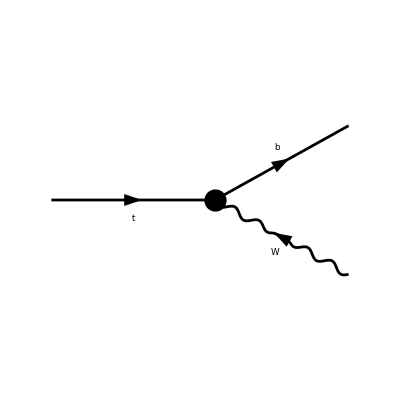

(ⅈ EL DiracMatrix[γ_μ,ℙL])/(√2 SW)

```mathematica
Module[{top,diags,amp},
top=CreateTopologies[0,1->2];
diags=InsertFields[top,{F[3,{3}]}->{F[4,{3}],-V[3]}];
Paint[diags,ColumnsXRows->{2,1},ImageSize->{200,100},Numbering->False];
amp=FeynArtsToX[CreateFeynAmp[diags,PreFactor->1,Truncated->True],IncomingMomenta->{P},OutgoingMomenta->{p1,p2,p3},LorentzIndices->{μ,ν}];
Total[amp]
]//ReplaceAll[{_SumOver->1,_IndexDelta->1}]
```

```mathematica
amp=Module[{top,diags,amp},
top=CreateTopologies[0,1->2];
diags=InsertFields[top,{F[3,{3}]}->{F[4,{3}],-V[3]}];
Paint[diags,ColumnsXRows->{2,1},ImageSize->{200,100},Numbering->False];
amp=FeynArtsToX[CreateFeynAmp[diags,PreFactor->1],IncomingMomenta->{P},OutgoingMomenta->{p1,p2,p3},LorentzIndices->{μ,ν}];
Total[amp]
]
```

-Graphics-

(ⅈ EL ⟨𝓊[p1,MB],γ_μ,ℙL,𝓊[P,MT]⟩ IndexDelta[Col1,Col2] (ℯ*[p2,MW])_μ SumOver[Col1,3,External] SumOver[Col2,3,External])/(√2 SW)

```mathematica
Sqrt[Kallenλ[MT^2,MW^2,MB^2]]/(16π*MT^3)1/2 AmplitudeInnerProduct[amp/.{_IndexDelta->1,_SumOver->1}]/.{P->p1+p2}//ReplaceAll[{p1.p1->MB^2,p2.p2->MW^2,p1.p2->(MT^2-MW^2-MB^2)/2}]//Simplify
```

(EL^2 (MB^4+MT^4+MT^2 MW^2-2 MW^4+MB^2 (-2 MT^2+MW^2)) √Kallenλ[MB^2,MT^2,MW^2])/(64 MT^3 MW^2 π SW^2)

```mathematica
Sqrt[Kallenλ[MT^2,MW^2,MB^2]]/(16π*MT^3)1/2 AmplitudeInnerProduct[amp/.{_IndexDelta->1,_SumOver->1}]/.{P->p1+p2}//ReplaceAll[{p1.p1->MB^2,p2.p2->MW^2,p1.p2->(MT^2-MW^2-MB^2)/2}]//Simplify//ToString[#,CForm]&//StringReplace[#,{"Power"->"pow","EL"->"sm_param::qe","MW"->"w_boson::mass","Γ"->"w_boson::width","ME"->"electron::mass","MM"->"muon::mass","Kallenλ"->"kallen_lambda","Sqrt"->"sqrt","MT"->"top_quark::mass","MB"->"bottom_quark::mass","SW"->"sm_param::sw"}]&
```

(pow(sm_param::qe,2)*(pow(bottom_quark::mass,4) + pow(top_quark::mass,4) + pow(top_quark::mass,2)*pow(w_boson::mass,2) - 2*pow(w_boson::mass,4) + pow(bottom_quark::mass,2)*(-2*pow(top_quark::mass,2) + pow(w_boson::mass,2)))*sqrt(kallen_lambda(pow(bottom_quark::mass,2),pow(top_quark::mass,2),pow(w_boson::mass,2))))/(64.*pow(top_quark::mass,3)*pow(w_boson::mass,2)*Pi*pow(sm_param::sw,2))

```mathematica
TheMass[F[3]]
```

MQU

#### μ^-->e^-ν_e ν_μ

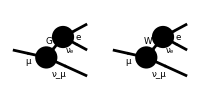

-1/(2 SW^2)ⅈ EL^2 ⟨𝓊[p1,ME],γ_ν,ℙL,𝓋[p2,0]⟩⊗⟨𝓊[p3,0],γ_μ,ℙL,𝓊[P,MM]⟩ (-((p1_μ+p2_μ) (p1_ν+p2_ν))/(MW^2 (-MW^2+ⅈ ImΣ[p1.p1+2 p1.p2+p2.p2,MW]+p1.p1+2 p1.p2+p2.p2))+(𝕘_(μ,ν))/(-MW^2+ⅈ ImΣ[p1.p1+2 p1.p2+p2.p2,MW]+p1.p1+2 p1.p2+p2.p2))

```mathematica
amp=Module[{top,diags,amp},
top=CreateTopologies[0,1->3];
diags=InsertFields[top,{Muon}->{Electron,-ENeutrino,MNeutrino}];
Paint[diags,ColumnsXRows->{2,1},ImageSize->{200,100},Numbering->False];
amp=FeynArtsToX[CreateFeynAmp[diags,PreFactor->1,GaugeRules->{_GaugeXi->ξ}],IncomingMomenta->{P},OutgoingMomenta->{p1,p2,p3},LorentzIndices->{μ,ν},PropagatorDenominatorFunction->(Den[#1,#2]&)];
amp=amp//ReplaceAll[Den[p_,√ξ*m_]:>1/ξ*Den[p/ξ,m]]//Series[#,{ξ,Infinity,0}]&//Normal//DeleteCases[#,0]&;
amp=amp//ReplaceAll[Den[p_,m_]:>1/(p.p-m^2+I*ImΣ[p.p,m])];
amp=amp//ReplaceAll[{ImΣ[0,m_]:>0}];
Total[amp]
]
```

```mathematica
AmplitudeInnerProduct[amp]//ReplaceAll[MandelstamRelations[{P,-p1,p2,p3,MM,ME,0,0}->{s,t,u}]]//ReplaceAll[Conjugate[t_ImΣ]:>t]//ReplaceAll[{t->MM^2+ME^2-s-u}]//ReplaceAll[{ImΣ[x_,m2_]:>m2*Γ}]//Simplify//ToString[#,CForm]&//StringReplace[#,{"Power"->"pow","EL"->"sm_param::qe","MW"->"w_boson::mass","Γ"->"w_boson::width","ME"->"electron::mass","MM"->"muon::mass"}]&
```

(pow(sm_param::qe,4)*(4*pow(w_boson::mass,4)*(pow(muon::mass,2) - s - u)*(s + u) + pow(electron::mass,4)*(-pow(muon::mass,4) + pow(muon::mass,2)*u) + pow(electron::mass,2)*(pow(muon::mass,4)*u + 4*pow(w_boson::mass,4)*(s + u) - pow(muon::mass,2)*(4*pow(w_boson::mass,4) + 4*pow(w_boson::mass,2)*s + pow(u,2)))))/(4.*pow(w_boson::mass,4)*pow(SW,4)*(pow(w_boson::mass,4) + pow(u,2) + pow(w_boson::mass,2)*(-2*u + pow(w_boson::width,2))))

#### e^+e^-->μ^+μ^-

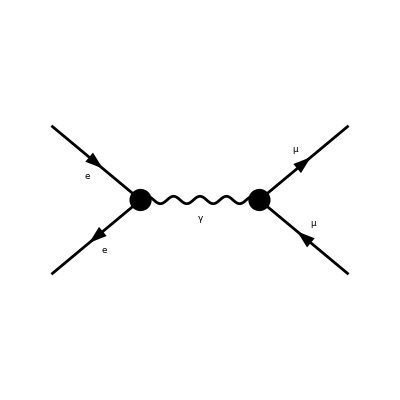

1/(p3.p3+2 p3.p4+p4.p4)ⅈ ⟨𝓋[p2,ME],ⅈ EL DiracMatrix[γ_μ,ℙL]+ⅈ EL DiracMatrix[γ_μ,ℙR],𝓊[p1,ME]⟩⊗⟨𝓊[p3,MM],ⅈ EL DiracMatrix[γ_ν,ℙL]+ⅈ EL DiracMatrix[γ_ν,ℙR],𝓋[p4,MM]⟩ 𝕘_(μ,ν)

```mathematica
amp=Module[{top,diags,amp},
top=CreateTopologies[0,2->2];
diags=InsertFields[top,{Electron,-Electron}->{Muon,-Muon},ExcludeParticles->{S,V[2]}];
Paint[diags,ColumnsXRows->{1,1},ImageSize->{200,100},Numbering->False];
amp=FeynArtsToX[CreateFeynAmp[diags,PreFactor->1],IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LorentzIndices->{μ,ν}]//Total
]
```

```mathematica
1/4 AmplitudeInnerProduct[amp]//ReplaceAll[MandelstamRelations[{p1,p2,p3,p4,ME,ME,MM,MM}->{s,t,u}]]//ToString[#,CForm]&//StringReplace[#,{"Power"->"pow","EL"->"sm_param::qe","MW"->"w_boson::mass","Γ"->"w_boson::width","ME"->"electron::mass","MM"->"muon::mass"}]&
```

(64*pow(sm_param::qe,4)*pow(electron::mass,2)*pow(muon::mass,2) + 16*pow(sm_param::qe,4)*pow(muon::mass,2)*(-2*pow(electron::mass,2) + s) + 16*pow(sm_param::qe,4)*pow(electron::mass,2)*(-2*pow(muon::mass,2) + s) + 8*pow(sm_param::qe,4)*pow(pow(electron::mass,2) + pow(muon::mass,2) - t,2) + 8*pow(sm_param::qe,4)*pow(pow(electron::mass,2) + pow(muon::mass,2) - u,2))/(4.*pow(s,2))